```mathematica
<<Util`
```

```mathematica
<<PSD`
```

```mathematica
ReadEventDat[fname_]:=Import[fname,"CSV"]
ReadEventMeta[fname_]:=Import[fname,"TSV"]⟦2;;⟧
ReadEventMetaColNames[fname_]:=Block[{tab},(tab[#⟦1⟧]=#⟦2⟧)&/@Transpose[{Import[fname,"TSV"]⟦1⟧,Range[Length[Import[datpath<>"/eventMD.tsv","TSV"]⟦1⟧]]}];
Return[tab]
]
DisplayEvents[eventMD_,eventTS_]:=
Manipulate[ListLinePlot[eventTS⟦i⟧,PlotRange->All,Epilog->{Black,Thick,Line[{{0,eventMD⟦i⟧⟦3⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦3⟧}}],Line[{{0,eventMD⟦i⟧⟦2⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦2⟧}}],Red,Line[{{eventMD⟦i⟧⟦4⟧,-400},{eventMD⟦i⟧⟦4⟧,400}}],Line[{{eventMD⟦i⟧⟦5⟧,-400},{eventMD⟦i⟧⟦5⟧,400}}]}],{i,1,Length[eventTS],1}]
```

```mathematica
Gauss1D[x_,α_,μ_,σ_]:=α Exp[-(x-μ)^2/(2 σ^2)]
```

```mathematica
ReadPyEventMeta[fname_]:=Block[{dat=Import[fname]⟦2;;⟧},
Return[Table[ToExpression[StringSplit[ToString[#],{"+/-"}]&/@dat⟦i⟧],{i,Length[dat]}]]
]
```

```mathematica
prange[dat_]:={All,0}/;Mean[dat]<0
prange[dat_]:={0,All}
```

```mathematica
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts⟦md⟦4⟧⟦1⟧-50;;md⟦5⟧⟦1⟧+50⟧,PlotRange->prange[ts],Frame->True,Epilog->{
Black,Thickness[Small],
 Line[{{0,md⟦2⟧⟦1⟧},{10000,md⟦2⟧⟦1⟧}}], Line[{{0,md⟦3⟧⟦1⟧},{10000,md⟦3⟧⟦1⟧}}], 
Red,Thickness[Small],
 Line[{{50-1,-500},{50-1,500}}],Line[{{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,-500},{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,500}}],
Blue,Text[Style[md⟦1⟧⟦1⟧,20],{50,txtpos}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts,PlotRange->prange[ts],Frame->True,PlotStyle->Gray,Epilog->{Red,Text[Style[md⟦1⟧⟦1⟧,20],{Length[ts]/2,txtpos}]}]
```

```mathematica
evnthist[ts_,md_]:=Show[{
ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,Frame->True,Epilog->{Black,Text[Style["o="<>ToString[md⟦2⟧⟦1⟧]<>"±"<>ToString[md⟦2⟧⟦2⟧]<>"\nb="<>ToString[md⟦3⟧⟦1⟧]<>"±"<>ToString[md⟦3⟧⟦2⟧],16],{70,0.02}]}],
Plot[Gauss1D[x,md⟦8⟧⟦2⟧,Abs[md⟦2⟧⟦1⟧],md⟦2⟧⟦2⟧]+Gauss1D[x,md⟦8⟧⟦1⟧,Abs[md⟦3⟧⟦1⟧],md⟦3⟧⟦2⟧],{x,0,150},PlotStyle->{Black,Thick}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evnthist[ts_,md_]:=ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,PlotStyle->Gray,Frame->True]
```

```mathematica
pydispevent[ts_,md_,txtpos_:-30]:=Manipulate[
GraphicsRow[{
evntplot[ts⟦i⟧,md⟦i⟧,txtpos],
evnthist[ts⟦i⟧,md⟦i⟧]
}],{i,1,Length[ts],1}
]
```

datpath = "/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/"

```mathematica
datpath="/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/"
```

/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/

```mathematica
pydispevent[ReadEventDat[datpath<>"/eventTS.csv"],ReadPyEventMeta[datpath<>"/eventMD.tsv"],-20]
```

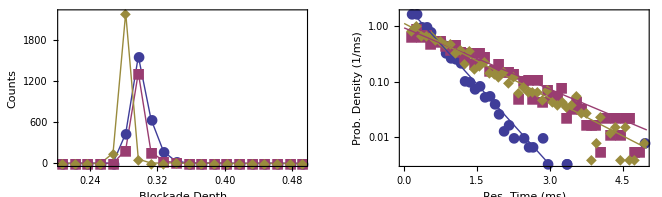

```mathematica
GraphicsRow[{
ListLinePlot[Evaluate[Hist1D[Select[ReadPyEventMeta[datpath<>"/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.2,0.5},0.015]&/@{"2012_09_10_0000","2012_09_10_0010","2012_09_10_0016"}],PlotRange->All,PlotMarkers->{Automatic,14},PlotStyle->Thick,Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Blockade Depth",18],Style["Counts",18]},Axes->False],
Show[
Show[{
ListLogPlot[Evaluate[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/"<>#<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,5},0.1]&/@{"2012_09_10_0000","2012_09_10_0010","2012_09_10_0016"}],PlotRange->All,Joined->False,PlotMarkers->{Automatic,14}],
LogPlot[Evaluate[{
Evaluate[Normal[NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/"<>"2012_09_10_0000"<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]]],
Evaluate[Normal[NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/"<>"2012_09_10_0010"<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]]],
Evaluate[Normal[NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/"<>"2012_09_10_0016"<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]]]
}],{t,0,5},PlotStyle->Thick]
}],Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Res. Time (ms)",18],Style["Prob. Density (1/ms)",18]}
]
}]
```

```mathematica
TableForm[{
Mean[Select[ReadPyEventMeta[datpath<>"/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]]&/@{"2012_09_10_0000","2012_09_10_0010","2012_09_10_0016"},
{
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0000/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"],
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0010/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"],
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0016/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"]
}
},TableHeadings->{Style[#,16,FontFamily->"TimesNewRoman"]&/@{"Blockade Depth","Res. Time (ms)"},Style[#,16,FontFamily->"TimesNewRoman"]&/@{"Pore 1 (blue)","Pore 2 (purple)","Pore 3 (olive)"}}]
```

| Pore 1 (blue) | Pore 2 (purple) | Pore 3 (olive)
Blockade Depth | 0.314403 | 0.303708 | 0.290694
Res. Time (ms) | 0.447308 | 1.17707 | 0.96295

```mathematica
goldpath="/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS"
```

/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS

```mathematica
pydispevent[ReadEventDat[goldpath<>"/eventTS.csv"],ReadPyEventMeta[goldpath<>"/eventMD.tsv"],{100,30}]
```

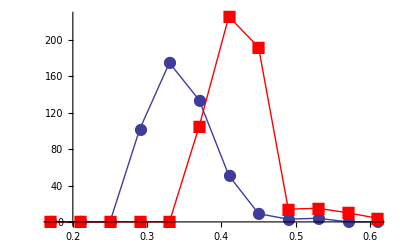

```mathematica
ListLinePlot[{
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD_low.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04],
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04]
},PlotRange->All,PlotMarkers->{Automatic,16},PlotStyle->{Thick,{Red,Thick}}]
```

```mathematica
Block[{ts=ReadEventDat["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventTS.csv"], md=ReadEventMeta["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventMD.tsv"]},
Manipulate[DisplayEvent[ts⟦i⟧,md⟦i⟧],{i,1,Length[ts],1}]
]
```

```mathematica
evnt⟦48⟧⟦;;5⟧
```

{-84.9027,-113.895,501,512,-102.786}

```mathematica
Manipulate[DisplayEvent[evnt⟦i⟧],{i,1,Length[evnt],1}]
```

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}
```

{113.143,113.841}

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}//Mean
```

113.492

```mathematica
DSolve[t''[x]+q/κ==0,t,x]
```

{{t→Function[{x},-(q x^2)/(2 κ)+C[1]+x C[2]]}}

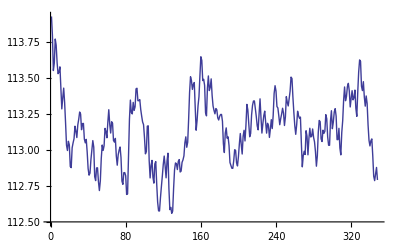

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]]
```

```mathematica
evnt⟦8⟧⟦4⟧
```

1091

```mathematica
evnt⟦8⟧⟦5;;⟧
```

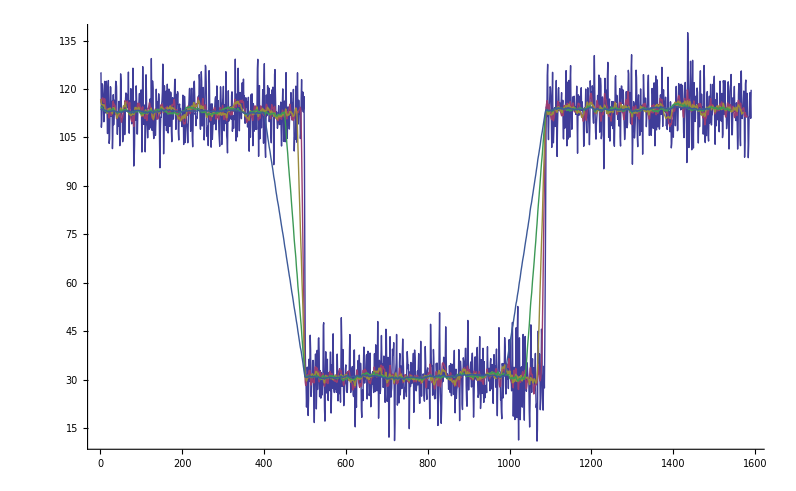

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;⟧],#]&/@{1,10,20,50,100},PlotRange->All]
```

```mathematica
DSolve[{D[f[t], t]==k c (1-f[t]/fmax)- kd f[t]},f[t],t]
```

{{f[t]→(c ⅇ^(((-c k-fmax kd) t)/fmax+((c k+fmax kd) t)/fmax) fmax k)/(c k+fmax kd)+ⅇ^(((-c k-fmax kd) t)/fmax) C[1]}}